```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/neerajsarna/sciebo/StaRMAP_ver1p9/SBP_Traditional/generic_2D/sbp_sat/plotting_routines

## solution data

```mathematica
M13 = Import["/Users/neerajsarna/sciebo/StaRMAP_ver1p9/SBP_Traditional/generic_2D/sbp_sat/gaussian_collision/result_n100_M13.txt","Table"];
```

```mathematica
GetRho[data_]:=Module[{rho},

rho= Table[{{data⟦1,ii⟧,data⟦2,ii⟧},data⟦3,ii⟧},{ii,1,Length[data⟦1⟧]}];

rho = Interpolation[rho]

]
```

```mathematica
GetVelocity[data_]:=Module[{ux,uy},

ux = Table[{{data⟦1,ii⟧,data⟦2,ii⟧},data⟦4,ii⟧},{ii,1,Length[data⟦1⟧]}];
uy = Table[{{data⟦1,ii⟧,data⟦2,ii⟧},data⟦5,ii⟧},{ii,1,Length[data⟦1⟧]}];

ux = Interpolation[ux];
uy = Interpolation[uy];

{ux,uy}
]
```

## plotting routines

```mathematica
CompareStreamLines[momSol_,dvmSol_,Mvalue_]:=Module[{},

StreamPlot[{{momSol⟦1⟧[x,y],momSol⟦2⟧[x,y]},{dvmSol⟦1⟧[x,y],dvmSol⟦2⟧[x,y]}},{x,0,1},{y,0,1},StreamPoints->{Automatic,0.1},ImageSize->Large,StreamStyle->{Red,Blue},PlotLegends->{Style[StringJoin["M=",ToString[Mvalue]],FontSize->14],Style["DVM",FontSize->14]},Frame->True,FrameTicksStyle->16]

]
```

```mathematica
PlotContours[momSol1_,momSol_,Mvalue_]:=Module[{plotDVM,plotMom},

plotDVM = ContourPlot[momSol1[x,y],{x,0,1},{y,0,1},ContourShading->None,ContourLabels->True,ContourStyle->Directive[Blue,Thick],Frame->True,FrameTicksStyle->Directive[Black,20],ImageSize->600,BaseStyle->{FontSize->15},FrameLabel->{{Style["y",FontSize->20],None},{Style["x",FontSize->20],None}},RotateLabel->False];

plotMom = ContourPlot[momSol[x,y],{x,0,1},{y,0,1},Frame->True,FrameTicksStyle->Directive[Black,20],ImageSize->600,BaseStyle->{FontSize->20},ContourStyle->Directive[Red,Thick],ContourShading->None,FrameLabel->{{Style["y",FontSize->20],None},{Style["x",FontSize->20],None}},RotateLabel->False];

Show[{plotMom,plotDVM}]

]
```

## Results

```mathematica
RhoM13 = GetRho[M13];
VelocityM13 = GetVelocity[M13];
```

```mathematica
contour=ContourPlot[RhoM13[x,y],{x,0,1},{y,0,1},ColorFunction->"TemperatureMap",ContourLabels->False,ContourLines->False,Frame->True,FrameTicksStyle->Directive[Black,20],ImageSize->600,BaseStyle->{FontSize->15},FrameLabel->{{Style["x_2",FontSize->20],None},{Style["x_1",FontSize->20],None}},RotateLabel->False,PlotLegends->BarLegend[Automatic,LabelStyle->{FontSize->16}],PlotLabel->Style["ρ̃(x_1,x_2,t=0.3)",FontSize->20,FontColor->Black]];

streamlines=StreamPlot[{VelocityM13⟦1⟧[x,y],VelocityM13⟦2⟧[x,y]},{x,0,1},{y,0,1},StreamPoints->{Automatic,0.05},ImageSize->Large,StreamStyle->{Black},Frame->True,FrameTicksStyle->16];
```

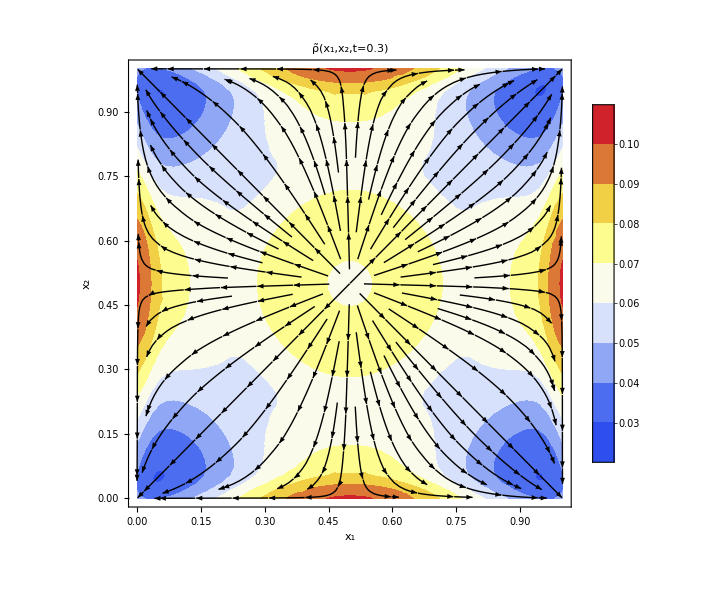

```mathematica
finalPlot=Show[{contour,streamlines}]
```

```mathematica
filename = "/Users/neerajsarna/Dropbox/my_papers/Publications/Comparitive_BC/results/gaussian_collision/rho.eps";
Export[filename,finalPlot]
```

/Users/neerajsarna/Dropbox/my_papers/Publications/Comparitive_BC/results/gaussian_collision/rho.eps